# Physics 230 -- Lab 7 (Programming I)

## Branton J. Campbell, BYU Physics & Astronomy, Winter 2010 Steve Turley, BYU Physics & Astronomy, Fall 2011

When carrying out a complicated task, we often need to evaluate multiple expressions in order to obtain a final result or sequence of results.  In previous labs, we have occasionally evaluated compound expressions on a single line, separated by semicolons, or performed multiple processing steps by nesting functions within functions or by composing them via postfix notation.  More often than not, we have simply evaluated more than one expression, each one on a separate line or in a separate cell, and assigned global names to each of the intermediate results.  However, some tasks are so complicated that this approach becomes impractical.  Any good computer "programming" language will include rules and operations that allow us to combine multiple single-step evaluations into a larger multi-step "program" that can perform an arbitrarily complex task with minimal user interaction.  In this lab, you will be introduced to several basic programming concepts.  Though the details will be specific to Mathematica, the concepts are quite general and have different implementations in other programming languages.

In this lab, we’ll learn about some powerful Mathematica functions which let you develop final results that require multiple steps.  These include logic to determine what steps to take, functions with different expressions in different regions, execution which depends on logical conditions, loops, and functions that are called recursively.  In the next lab, we’ll learn how to peice these together into yet more complex programs.

## Logic (20 min)

The "binary" number system has base 2 rather than base 10.  The binary integers within this system consist of the set containing 0 and 1.  A "logical" variable can have one of two discrete values, True or False.  Because there is an obvious connection between such a two-value system and the binary integers, we often associate 0 → False and 1 → True.  A "binary" function takes two inputs and returns one output.  In this context, the word "binary" refers to the number of inputs rather than the type of inputs.  A "binary logic function" takes two logical (i.e. True or False) inputs and returns one logical output.  You have encountered these before in the context of digital electronics, where 0 Volts → False and 5 Volts → True.

### (#1) Binary logic functions (15 min)

(a) Use Mathematica's BaseForm function to convert the decimal integers 0 through 16 in binary form.  Explain to your TA how 1001_2 = 9_10.

```mathematica
Manipulate[BaseForm[i,2],{i,0,16,1}]
BaseForm[67,2]
BaseForm[15,2]
```

1000011_2

1111_2

(b) You can convert from binary from back to an integer using FromDigits.

```mathematica
FromDigits[{1,0,1,1,1},2]
```

23

It also works with strings.

```mathematica
FromDigits["10111",2]
```

23

Sometimes you will receive encoded information from an instrument,where a set bit or sequence of bits indicates a condition and a slice of information.   Suppose your instrument documentation said the instrument returned a status byte (integer) that had bits with the following meaning:

bit 0: set (i.e. 1) if data is ready
bits 1-4: channel with information
bit 5: set if there was an overflow condition
bit 6: set if device is within temperature limits
bit 7: set if device is within pressure limits

You can use the BitAnd, BitShiftRight, and other Bitwise Operations to test the status of the various bits.

Here are some expressions you could use to test a status you received of status code fo 103.  Execute the cell and explain how they work to your TA.

```mathematica
status = 103;
BaseForm[status,2]
dataIsRead = BitAnd[status, 2^0]>0
channel = BitShiftRight[BitAnd[status, FromDigits[{1,1,1,0},2]],1]
overflow = BitAnd[status, 2^5]>0
withinTemperatureLimits = BitAnd[status, 2^6]>0
withinPressureLimits = BitAnd[status, 2^7]>0
```

1100111_2

True

3

True

True

False

(c) Binary logic functions such as And, Or, Nand, Nor and Xor are summarized on the DC guide page on Logic and Boolean Algebra.  Take a few minutes to become familiar with the shorthand notation for each of these operations.  The only single-input logic function that you need to be familiar with is Not.  You can practice them in the cell below.

(d) See the tutorial on Relational and Logical Operators to review the relational operators available in Mathematica.  Write a function that will return true if a value is postive and prime or negative and even.  Test it by mapping it to the list tList below.  You might find PrimeQ, EvenQ, and Map helpful.

```mathematica
tList={-6,0,5,9,14}
theTest[number_]:=Module[{},
a = PrimeQ[number];
b = number>0;
c = EvenQ[number];
d = number <0;
a&&b||c&&d]
theTest/@tList
```

{-6,0,5,9,14}

{True,False,True,False,False}

### (#2) Inequalities (5 min)

See the tutorial on Relational and Logical Operators to review the relational operators available in Mathematica.  Evaluate the cell below to Simplify several combined inequalities.  Explain the output to your TA.

```mathematica
Simplify[(x>y)&&(x<y)]
Simplify[(x>y)&&(x≥y)]
Simplify[(x≥y)&&(x≤y)]
Simplify[(x>y)||(x<y)]
Simplify[(x>y)||(x≥y)]
Simplify[(x≥y)||(x≤y)]
```

False

x>y

x==y

x≠y

x≥y

True

## Piecewise Functions (20 min)

A piecewise functions is a function whose definition is different in different domains of its independent variable.  You have encountered the Piecewise and Boole functions in previous lab exercises, though we didn't take time to formally introduce them.  They allow us to define arbitrary piecewise functions (even multidimensional functions) based on a set of inequalities.  You have also worked with a number of pre-defined piecewise functions such as Abs and Sign.

### (#3) Built-in piecewise functions (10 min)

(a) Evaluate the cell below to define a list of common piecewise functions.  Links to their DC reference pages are found on the Conditionals guide page in the section on Mathematical Function Conditionals.

```mathematica
funclist = {Round, Floor, Ceiling, IntegerPart, FractionalPart, Abs, Sign,UnitStep,Unitize,Chop[#,1]&, Clip}
```

{Round,Floor,Ceiling,IntegerPart,FractionalPart,Abs,Sign,UnitStep,Unitize,Chop[#1,1]&,Clip}

(b) Plot each of these piecewise functions over the range {x, -3, 3} with {PlotRange → All, ExclusionsStyle → Automatic, PlotLabel → #, PlotStyle → Thick} as options.  Do this with one line of code by creating a pure function (where the function name is the variable) and then mapping it onto the list of function names.  If you still aren't comfortable with pure functions, then spend some time and get comfortable.  Explain each graph to your TA.

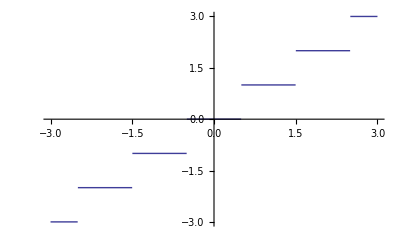

```mathematica
plotFunc [i_]:=Plot[funclist[[i]][x],{x,-3,3},PlotRange -> All, ExclusionsStyle -> Automatic, PlotLabel -> funclist[[i]], PlotStyle -> Thick]
Manipulate[plotFunc[j],{j,1,11,1}]
Plot[Round[x],{x,-3,3}]
```

### (#4) General piecewise functions (10 min)

(a) Use Piecewise to define an expression that equals 1/6(2+x)^3 over the range -2<x≤-1,  1/6(4-6 x^2-3 x^3) over the range -1<x≤0,  1/6(4-6 x^2+3 x^3) over the range 0<x≤1,  1/6(2-x)^3 the range 1<x≤2, or 0 otherwise.  This curve is called a uniform cubic B-spline.  Compute the 1^st, 2^nd and 3^rd derivatives of the B-spline and also the indefinite integral of the B-spline, giving each result a different name.

```mathematica
myfuncfor4 = Piecewise[{{0,x≤-2},{1/6(2+x)^3,-2<x≤-1},{1/6(4-6 x^2-3 x^3),-1<x≤0},{1/6(4-6 x^2+3 x^3),0<x≤1},{1/6(2-x)^3,1<x≤2},{0,x>2}}];
d1st = D[ myfuncfor4,{x,1}]
d2nd = D[ myfuncfor4,{x,2}]
d3rd = D[ myfuncfor4,{x,3}]
indefint = Integrate[myfuncfor4,x]
thelist = {myfuncfor4,d1st,d2nd,d3rd,indefint};
```

Piecewise[{{0, x<-2||x==-2}, {1/2 (2+x)^2, -2<x<-1}, {1/2, x==-1}, {1/6 (-12 x-9 x^2), -1<x<0}, {0, x==0}, {1/6 (-12 x+9 x^2), 0<x<1}, {-1/2, x==1}, {-1/2 (-2+x)^2, 1<x<2}, {0, True}}]

Piecewise[{{0, x<-2||x==-2}, {2+x, -2<x<-1}, {1, x==-1}, {1/2 (-4-6 x), -1<x<0}, {-2, x==0}, {1/2 (-4+6 x), 0<x<1}, {1, x==1}, {2-x, 1<x<2}, {0, True}}]

Piecewise[{{0, x<-2}, {1, -2<x<-1}, {-3, -1<x<0}, {3, 0<x<1}, {-1, 1<x<2}, {0, x>2}, {Indeterminate, True}}]

Piecewise[{{0, x≤-2}, {1/24 (2+x)^4, -2<x≤-1}, {1/2+(2 x)/3-x^3/3-x^4/8, -1<x≤0}, {1/2+(2 x)/3-x^3/3+x^4/8, 0<x≤1}, {1-1/24 (-2+x)^4, 1<x≤2}, {1, True}}]

(b) Group the B-spline, its first three derivatives and its indefinite integral into a list, and then Plot them all (on separate graphs), over the range {x, -3, 3} with {PlotRange→All, ExclusionsStyle→Automatic} as options.

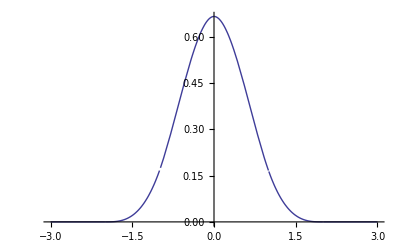
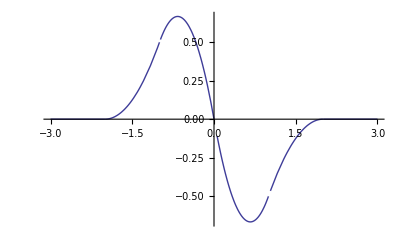
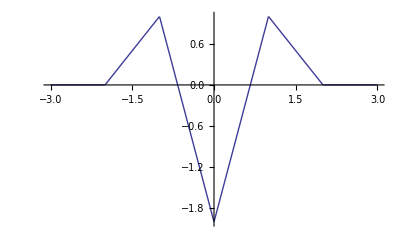
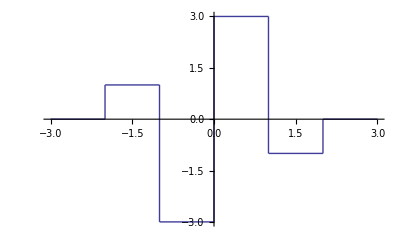
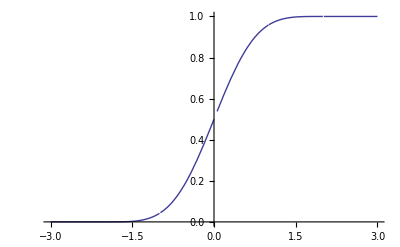

```mathematica
Table[Plot[thelist[[n]],{x,-3,3},PlotRange->All,ExclusionsStyle->Automatic],{n,1,5}]
```

(c) Finally, compute the definite integral of the B-spline from x = -3 to +3.

```mathematica
Integrate[myfuncfor4,{x,-3,3}]
```

1

## Conditional decisions (25 min)

The conditionals addressed here must decide amongst multiple outputs based on a logical test against the input.  If selects between two possible outputs based on a single logical (i.e. True/False) input.  Which evaluates multiple logical inputs, but only returns the output corresponding to the first True input.  Switch compares an expression against multiple patterns, but only returns the output corresponding to the first pattern that matches the expression.  The DC guide on Conditionals may prove to be a useful reference.

### (#5) "If" (15 min)

(a) Use If (not Piecewise) to define a piecewise function, myabs[x_], that mimics the Abs function.  Plot it over the range from {x, -3, 3}.

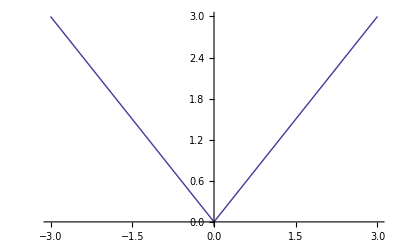

```mathematica
myabs[x_]:=If[x<0,-x,x]
Plot[myabs[x],{x,-3,3}]
```

(b)  Use If to create a function (named surprise) that takes no arguments, but randomly returns either a 0 or a 1, with 0 appearing 2/3 of the time and 1 appearing 1/3 of the time.  Hint: a RandomReal number between 0 and 1 has a 2/3 probability of being less than 2/3.  After you get it working properly, create a list of 10^4 surprise values and verify that their average is approximately 1/3.

```mathematica
surprise:= If[RandomReal[]<2/3,0,1]
biglist =Table[surprise,{n,0,10^4}];
Mean[biglist]//N
```

0.334367

(c) Use If to create a function, happyprime[n_], the returns a  when n is a prime number and a  otherwise (you can copy/paste these icons into your function).  Then try it out on the integers from 1 to 10.

```mathematica
happyprime[n_]:= If[PrimeQ[n],-Graphics-,-Graphics- ]
happyprime/@Range[1,10,1]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### (#6) "Which" (10 min)

Use Which (not Piecewise) to define a piecewise function myspline[x_] that is equivalent to the cubic B-spline defined above in a previous exercise.  Make sure that you handle cases where |x|>2.  Plot your function over the range from {x, -3, 3}.  You might be able to copy/paste/modify some code from a previous exercise.

```mathematica
pwfunc = Piecewise[{{0,x≤-2},{1/6(2+x)^3,-2<x≤-1},{1/6(4-6 x^2-3 x^3),-1<x≤0},{1/6(4-6 x^2+3 x^3),0<x≤1},{1/6(2-x)^3,1<x≤2},{0,x>2}}];
```

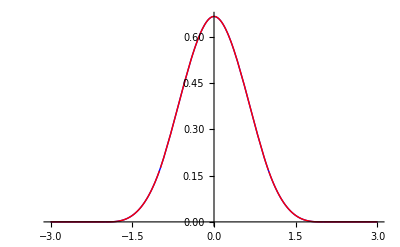

```mathematica
whichfunc = Which[Abs[x]>2,0,-2<x≤-1,1/6(2+x)^3,-1<x≤0,1/6(4-6 x^2-3 x^3),0<x≤1,1/6(4-6 x^2+3 x^3),1<x≤2,1/6(2-x)^3];
Plot[{whichfunc,pwfunc},{x,-3,3},PlotStyle->{{Blue,Thick},{Red,Thin}}]
```

## Procedural loops (40 min)

Loop structures allow us to sequentially run though a list of similar evaluations.  Examples might include counting to 10, performing a finite sum, performing the same operation on each element of list, or iteratively searching for the numerical solution to a nonlinear equation.  In this section, we will introduce several procedural loop structures (Do, While and For).  As expected from a "procedure", they can each perform global-variable assignments, but produce no outputs.

### (#7) Compound expressions as function arguments (5 min)

(a) A series of expressions separated by semicolons is called a "compound expression".  We have often used this construct to perform multiple computations on a single line, but only display the last result.  Evaluate the example below to see how a CompoundExpression is viewed internally by Mathematica.  Observe that the first two simple expressions (M = 2 and Q = 3^M) do get evaluated, but that only the second simple expression (5 Q) is "returned" to Mathematica as output.  In general, when we string multiple simple expressions together into a compound expression, only the last one gets returned as output.  Reread that last sentence for emphasis!

```mathematica
M = 2; Q = 3^M; 5*Q 
Hold[M = 2; Q = 3^M;5*Q]//FullForm
```

45

Hold[CompoundExpression[Set[M,2],Set[Q,Power[3,M]],Times[5,Q]]]

(b) Up to now, compound expressions were simple matter of convenience and probably don't seem very important.  In the context of programming, however, compound expressions are an essential part of the Mathematica language.  In fact, any argument that you feed to any Mathematica function can be replaced with a compound expression.  Reread that last sentence three times for emphasis!

Evaluate the cells below to see two equivalent definite integrals, and observe that the second case employs compound expressions.  In both cases, Integrate takes two arguments.  Thus, it should be clear that semicolons do not separate function arguments -- only commas can do that.  Also observe that ONLY the last simple expression within each compound expression actually gets returned to Integrate as a proper argument.  Describe this in detail to your TA.

```mathematica
Integrate[x^2,{x,0,1}]
```

1/3

```mathematica
Integrate[base = x; exponent = 2; base^exponent, {x,0,1}]
```

1/3

(c) Use a compound expression in the first argument of NSum to compute a numerical result for ∑ _(n=1)^∞ (ln(n))/n^4.  Hint: define the numerator and demoninator separately and then combine them in one big compound expression.

```mathematica
Sum[numerator=Log[n];denominator=n^4;numerator/denominator,{n,1,∞}]
```

-Zeta'[4]

### (#8) Special assignment shortcuts (5 min)

Though Mathematica provides a handful of assignment functions, which have been specifically designed to modify their arguments, the vast majority of Mathematica functions do not modify their arguments.  Here, we will experiment with some Special Forms of Assignment, which are especially useful for modifying variables within a program.  The syntax of these assignments parallels similar syntax in the C and Java languages.

(a) Evaluate and study the following examples of the Increment (r++) PreIncrement (++r ), Decrement (r--) and PreDecrement (--r ) functions.  Observe that while all of these functions update the value of their argument, both Increment and Decrement return the old pre-update value as output.

```mathematica
r=0;
r++
r
```

0

1

```mathematica
r=0;
++r
r
```

1

1

```mathematica
r=0;
--r
r
```

-1

-1

```mathematica
r=0;
r--
r
```

0

-1

(b) Evaluate the cell below, and make sure that you understand how each of the following assignments changes the value of r.

```mathematica
r = 2
r*= 3
r+= 7
r-= 1
r/=4
```

2

6

13

12

3

### (#9) "Do" (10 min)

Mathematica's Do loop is much like the Do implemented in the Fortran language.  It has a locally-defined iterator (with specified range and stepsize), and terminates when the iterator has traversed its range.

(a) Evaluate the cell below and observe that a Do loop doesn't actually return any output.  Null isn't really proper output -- just a placeholder that pops out when nothing else is returned.

```mathematica
Do["any expression that you can imagine",{n,1,10}]
%//FullForm
```

Null

(b)   Evaluate the example below, which uses a global variable (result) to compute the sum of the integers from 1 to 10.  We check result at the end to verify that it becomes 55 as expected.

```mathematica
result = 0;
Do[result+=n,{n,1,10}]
result
```

55

(c) In the cell below, pull all of the code from the previous cell onto a single line using a compound expression.

```mathematica
result = 0;Do[result+=n,{n,1,10}];result
```

55

(d) Use Do to start with decimal number latest = 1.0, and recursively compute 100 cosines, taking the cosine of the most recent result each time.  Show the final value of latest.

```mathematica
latest=1.0;Do[latest=Cos[latest],{100}];latest
```

0.739085

(e) In this example, we use nested Do loops to accumulate a list of the integer sums of the form ∑ _(n =1)^p n  for p values running from 1 to 10.  Evaluate the example and figure out how it works.  Then modify them to accumulate a list of the squared-integer sums of the form  ∑ _(n =1)^p n^2.  You might want to copy the code to a practice cell first.

```mathematica
reslist = {}; result=0;Do[ result+=p;reslist = Append[reslist,result], {p,1,10}];reslist
reslist2 = {}; result=0;Do[ result+=p*p;reslist2 = Append[reslist2,result], {p,1,10}];reslist2
```

{1,3,6,10,15,21,28,36,45,55}

{1,5,14,30,55,91,140,204,285,385}

### (#10) "While" (10 min)

Mathematica's While loop is much like the While or Do/While loops that you may have seen in other programming languages.  It has no iterator, but terminates when some condition is met.

(a) Evaluate the example below, where we use While to find the largest Prime number less than 10^6.  We use the global variable m as an iterator.

```mathematica
m = 1;While[Prime[m]<10^6,m++]; Prime[m-1]
```

999983

(b) Start with decimal number latest = 1.0, and use While to recursively compute cosines until the magnitude of the change between recursions is less than 10^-6.  In other words, keep evaluating  latest = Cos[latest] as long as Abs[Cos[latest]-latest] >10^-6.  Use a second global variable to count the number of iterations required.  Then compare latest to the result that you previously obtained with a Do loop.

```mathematica
Clear["`*"]
```

```mathematica
latest = 1.0;Abs[Cos[latest]-latest] > 1*^-6
```

True

```mathematica
latest= 1.0;n=0 ; While[Abs[Cos[latest]-latest]>1*^-6,latest = Cos[latest];n++];{latest,n}
```

{0.739085,33}

### (#11) "For" (10 min)

Mathematica's For loop is much like the For implemented in the C and Java languages.  It has an global iterator variable, a mechanism for changing the iterator, and a condition on the iterator that terminates the loop.  Most tasks that you can accomplish with For, you can also accomplish with either Do or While loop.

(a)  Evaluate the example below, where we use For to identify all of the integers less than or equal to 25 that have an odd number of 1's in their binary (i.e. base-2) representations.

```mathematica
oddones[n_] := OddQ[Count[IntegerDigits[n,2],1]]
For[n=1,n≤25,n++,If[oddones[n],Print[{n,BaseForm[n,2]}]]]
```

{1,1_2}

{2,10_2}

{4,100_2}

{7,111_2}

{8,1000_2}

{11,1011_2}

{13,1101_2}

{14,1110_2}

{16,10000_2}

{19,10011_2}

{21,10101_2}

{22,10110_2}

{25,11001_2}

(b) In the cell below, use For to compute a list of each of the powers of 2 (i.e. 2^n) less than 10^6.  Hints: First define reslist = { } for future use.  Then, for every non-negative integer n such that 2^n<10^6, use AppendTo to append 2^n to reslist.

```mathematica
reslist={};
For[n=0,2^n < 1*^6,n++,AppendTo[reslist,2^n]];reslist
```

{1,2,4,8,16,32,64,128,256,512,1024,2048,4096,8192,16384,32768,65536,131072,262144,524288}

## Recursive Structures (15 min)

You are already familiar with several of Mathematica's functional loop structures (e.g. Table, Sum, NIntegrate, Plot, Map, etc.) which either iterate over fixed range of numbers or over the elements of a list.  As expected of a "function", they each take input and produce output, but don't alter any global variables.  In this section, we introduce several new functional loop structures that are designed for recursive function evaluation.  The guide page on Functional Iteration is a useful quick reference to these functions.

### (#12) Nest and NestList (10 min)

(a)  Evaluate the cell below to observe the behavior of Nest.  The function starts with 0 as input and recursively adds 1 to the previous result for a total of 10 recursions. Explain to your TA how this example works.

```mathematica
Nest[#+1&,0,10]
```

10

(b) Use Nest to start with the decimal number 1.0, and recursively compute 100 cosines.  Compare your output to the result that you previously obtained with a Do loop.

```mathematica
ne = 1.0; Nest[Cos[#]&,ne,100] (* same answer as above two examples *)
```

0.739085

(c) Sometimes it’s helpful to see how the nested calculations are progressiong at each step.  A convenient function to use for this is NestList.  It not only gives a final result, but produces a list which includesall of the intermediate results as well.  Repeat the calculation you did in part (b) using NestList instead of Nest and compare the results.

```mathematica
ne = 1.0; NestList[Cos[#]&,ne,100]
```

{1.,0.540302,0.857553,0.65429,0.79348,0.701369,0.76396,0.722102,0.750418,0.731404,0.744237,0.735605,0.741425,0.737507,0.740147,0.738369,0.739567,0.73876,0.739304,0.738938,0.739184,0.739018,0.73913,0.739055,0.739106,0.739071,0.739094,0.739079,0.739089,0.739082,0.739087,0.739084,0.739086,0.739085,0.739086,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085}

### (#13) NestWhile (5 min)

(a) NestWhile is similar to Nest , but does not take a prespecified number of recursions.  Instead, it terminates using a logical condition that depends on the evolving value of the output.  After each recursion, the value of the output is tested against the condition.  As long as the condition returns True, the recursions continue.  When the condition finally returns False, the recursions stop and a final output value is returned.  Evaluate the two examples in the cell below, and explain to your TA how they work.

```mathematica
NestWhile[#+1&,0,#<10&]
```

10

(d) Use NestWhile to start with the decimal number 1.0, and recursively compute cosines until the magnitude of the change between recursions is less than 10^-6.  In other words, keep recursing as long as Abs[Cos[#] - #] >10^-6 & .  Compare the final value to the result that you previously obtained with While.  If you are still uncomfortable with pure functions, it's time to get comfortable now.  Seriously.  Don't go on until you understand them.

```mathematica
nes = 1.0; NestWhile[Cos[#]&,nes,Abs[Cos[#]-#] > 1*^-6 &]
```

0.739085

### Other recursive functions (optional)

The guide page on Functional Iteration lists other recursive functions.  We will learn more about FixedPoint in the next lab.  Evaluate the cell below to see one interesting example of Fold, which we modified from an example at the end of the tutorial on Applying Functions Repeatedly, and which achieves the same functionality as Mathematica's FromDigits function with integer input.

```mathematica
mytry[digitlist_,base_]:=Fold[base*#1+#2&,0,digitlist]
mytry[{a,b,c,d,e,f,g},10]
%//Expand

mytry[{1,0,4,8,5,7,6},10]
FromDigits[{1,0,4,8,5,7,6},10]
```

10 (10 (10 (10 (10 (10 a+b)+c)+d)+e)+f)+g

1000000 a+100000 b+10000 c+1000 d+100 e+10 f+g

1048576

1048576

## Programming Paradigms (10 min)

### (#14) Speed and Convenience (10 min)

As you've no doubt noticed there are usally many ways to solve the same problem in Mathematica.  So with many different ways to choose to do things, how do you decide which is "best?"  Here are some of the factors you might want to consider.

You should choose an approach which is as clear as possible both to you and to others who may use your program later.

If you do a similar thing in a number of places in your code, use a common function to do it.  That way, if you find a problem and need to change it, you only have to do so in one place.

Sometimes one way of accomplishing a task can take dramatically more memory or time than another way.  If the time starts to get long enough to be noticable or the memory needs limit what you can do in the calculation, consider alternate approaches which may be less demanding on the computer resources.

If there is a Mathematica function which already does what you want to do, it is usually faster and clearer to use it than to write your own.

Here is an example of several ways to find the mean (average) values of a large number of random real numbers.  A fast, compact way to do so is to generate a list of numbers with a single call to RandomReal and then use the Mean function.

```mathematica
nvals=1000000;
```

```mathematica
Timing[Mean[RandomReal[{-1,1},nvals]]]
```

{0.031,-0.0000410758}

A noticeable slower way to do the same thing would be to generate the random numbers individually within a Table statement or a loop.

```mathematica
Timing[vals=Table[RandomReal[{-1,1}],{i,1,nvals}];
sum=0;
For[i=1, i≤nvals, i++, sum +=vals[[i]]];
sum/nvals]
```

{3.432,0.00105408}

```mathematica
Timing[
sum=0;
For[i=1, i≤nvals, i++,sum += RandomReal[{-1,1}]];
sum/nvals
]
```

{3.245,-0.000569269}

{3.682,0.000784174}

On the other hand, if you have a much larger number of random numbers, you will run out of memory trying to generate a list of all of them.  In this case, your only alternative is to create them in smaller chunks.

```mathematica
nvals=100000000
```

100000000

100000000

```mathematica
Timing[Mean[RandomReal[{-1,1},1000000000]]]
```

No more memory available.
Mathematica kernel has shut down.
Try quitting other applications and then retry.

```mathematica
(* reset nvals since we have quit the kernel *)
nvals = 100000000
Timing[
sum=0;
(* Assume nvals is a multiple of 1000000, otherwise this fails *)
loops=nvals/1000000;
For[i=0, i<loops, i++, sum+= Mean[RandomReal[{-1,1},1000000]]];
sum/loops
]
```

{2.667,0.0000120852}

100000000

100000000

{2.387,4.11394×10^-6}

We could have also done this with single function evaluations, but it would have been much slower.

To illustrate the value of using internal Mathematica functions to do a task, consider finding the numerical integral of f x=1/(log(sin(5 x)+21/10)) between 0 and 40.

```mathematica
f14[x_]:=1/Log[21/10+Sin[5*x]]//N[#,20]&
```

First compute this integral using NIntegrate and Timing.  Use a PrecisionGoal of 7 and a WorkingPrecision of 20.

```mathematica
Timing[NIntegrate[f14[x],{x,0,40}]]
```

{0.062,105.09}

Now time how long it takes to compute this using the mid-point rule.  For an integral from x_i to x_f , the midpoint rule approximates the integral using n-point Riemann sums as follows:
dx=(x_f-x_i)/n
(∫^x_f)_x_i f(x)ⅆx=dx∑_(i=0)^(n-1) f(x_i+dx(i+1/2))

```mathematica
reimann[n_]:=Timing[40/n*Sum[f14[0+40/n*(i+1/2)],{i,1,n}]] (*don't get this one*)
reimann[200000]
```

{88.078,105.09093251939886567}

How many points are required to get 6 significant digits?

How do the timings compare?

## Working on Your Own (30 min)

### (#15) Atomic Beam (15 min)

You create a beam of sodium atoms by heating them up in an oven with a 4 mm slit as shown in the diagram below.  The beam is collimated with another slit 20 cm away which also has a width of 4 mm.  One meter later, the atoms are detected by illuminating them with a resonant laser beam 2 mm wide and monitoring the fluorescense.  Plot the intensity of the fluorescence signal seen at the end of the beam.  Note that all of the angles in this problem are small enough to use the small angle approximation (sin(θ)=tan(θ)=θ).

HINT : Assume the atoms leave the first slit with an equal probability of going any direction from any point in the slit.  (This isn’t strictly true, but it’s a good approximation in this case.)  You will find a condition expression or piecewise function good ways to represent this beam.  If you look back at the first slit from the fluorescense point, the intensity of the beam will be proportional to the amount of the first slit that you can see through the second slit at that point.

The fluorescense signal is the integral of the product of the rectangular laser beam and the fraction of the atomic beam it illuminates at each angle.

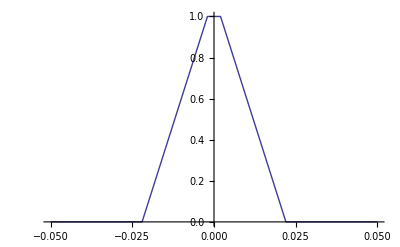

```mathematica
intensity[x_]:=  Which[Abs[x]>.022,0,-.022≤x<-.002,50*x+1.1,-.002<x<.002,1,.002≤x<.022,-50*x+1.1]
Plot[intensity[x],{x,-.05,.05}]
```

```mathematica
Clear[intensity]
```

### (#16) Finite Square Well (15 min)

The finite square is a quantum mechanics problem which only has a numerical solution for the energy.  We got an approximate solution earlier using the variational principle.  Here we will find an arbitrarily precise solution.

Assume we have a particle in a potential well which is 0 between -1 and 1 and 3 outside this region.  We’ll choose units where the mass of the particle is 1 and Plank’s constant is also 1.  If we are interest in the lowest energy state, the wave function inside the well must have the form ψ(x)=c1 cos(k x) where k=√(2 e)  with e being the energy of the particle.  For our purposes, the normalization of the wave funciton doesn’t matter and we can just set c1=1.  Write a function for the wave function ψ(x) and the potential energy v(x) and plot these on the same graph.  Use a value of 1 for k at this point until we can find something better.

```mathematica
energy [x_]:= Which[-1<x<1, 0, Abs[x]≥ 1, 3];
ψ[x_]:= Cos[x]
```

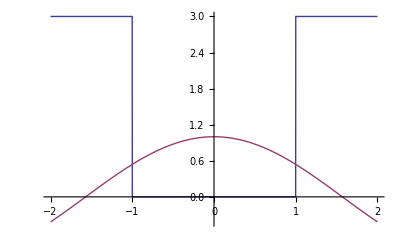

```mathematica
Plot[{energy[x],ψ[x]},{x,-2,2}]
```

In the region where Abs[x]>1, the wave function has the form ψ(x)=c2 exp(-α Abs[x]) where α=√(2 (3-e)).  Plot the potential energy and ψ for this case on the same graph.

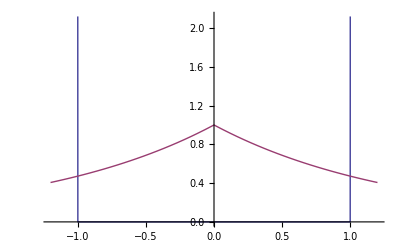

```mathematica
Plot[{energy[x],Exp[-√(2*(3-Exp[1]))*Abs[x]]},{x,-1.2,1.2}]
```

Quantum mechanics requires the the function on the inside of the well and the function outside the well need to join smoothly and have a continuous first derivative.  In other words, the following two equations have to be true at the point x=1.

cos(k)==c2 exp(-α)
-k sin(k)==-α c2 exp(-α)

Multiplying the second equation by -1 and dividing by the first equation, one gets

k tan(k)==α

If we square both sides of this equation and substitute in the expressions for k and α we can write this equation as

k^2 tan^2(k)==2 (3-e)==2 (3-k^2/2) (*where did get get that e = k^2/2? *)

Simplifying this expression yields

-k^2/2-1/2 k^2 tan^2(k)+3==0

#### Solution using FindRoot

This equation can be easil solved using FindRoot.   Go ahead and do so to give us a check on another method.  Find root will require an initial guess for k.  You can generate on by looking at a graph of the function f(k)=-k^2/2-1/2 k^2 tan^2(k)+3.

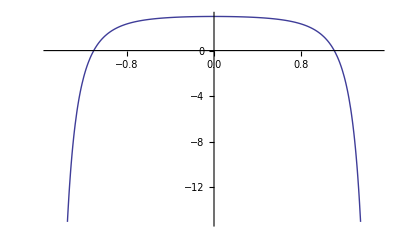

{k→1.10348}

```mathematica
Plot[-k^2/2-1/2 k^2*(Tan[k])^2+3,{k,-1.5,1.5}]
FindRoot[-k^2/2-1/2 k^2*(Tan[k])^2+3,{k,1}]
```

#### Solution using the Newton-Raphson Method

Just for fun ( and to give you some practice with NestWhile), let’s also solve this equation using the Newton-Raphson method.  In our case, we are trying to solve the equation f(k)=-k^2/2-1/2 k^2 tan^2(k)+3=0, Consider the Taylor series expansion of f(k) at a point k_0  in the neighborhood of k, which k is the point where f(k)==0.  We then have

f(k)==0==(k-k_0) f'(k_0)+f(k_0)

If we let δ==k-k_0 be the correction we want to make to k for a better estimate, then the above equation can be solved for δ.

δ=-f[k_0]/f'[k_0]

If we recursively make this correction to k_0   its value will get closer and closer to the true value of k we seek.

Here’s an example of using the Newton-Raphson method to solve the equation cos(x)-x==0  we have solved a few times already in this lab.  We’ll ask for about 7 digits of accuracy in the answer.

```mathematica
f[x_]:=Cos[x]-x
NestWhile[#-f[#]/f'[#]&,1.,Abs[f[#]]>10^-7&]
```

0.739085

Use this technique to find the value of k which solves the equation  f(k)=-k^2/2-1/2 k^2 tan^2(k)+3.

```mathematica
g[x_]:=-x^2/2-1/2 x^2*(Tan[x])^2+3
NestWhile[#-g[#]/g'[#]&,1,Abs[g[#]] > 1*^-7 &]//N
```

1.10348

How does this answer compare to the one you got using FindRoot?